## Single joint, flexible link (robotics), Problem 11.16

```mathematica
Clear["Global`*"];
```

```mathematica
eq1=Subscript[θ, 1]''[t]+Sin[Subscript[θ, 1][t]]+Subscript[θ, 1][t]-Subscript[θ, 2][t]==0;
eq2=Subscript[θ, 2]''[t]-Subscript[θ, 1][t]+Subscript[θ, 2][t]==u[t];
asys0=AffineStateSpaceModel[{eq1,eq2},{Subscript[θ, 1][t],Subscript[θ, 2][t]},u[t],Subscript[θ, 1][t],t];
asys=AffineStateSpaceModel[asys0,({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, 3]}, {Subscript[x, 4]}})]  (* get nice labels *)
(* steady-state output *)
```

x_2[t]-Sin[x_1[t]]-x_1[t]+x_3[t]x_4[t]x_1[t]-x_3[t]0001x_1[t]0x_1[t]x_2[t]x_3[t]x_4[t]411111NoneFalseFalseFalseFalse{{u[t],0}}t

```mathematica
SystemsModelVectorRelativeOrders[asys]  (* # of times to diff. before u[t] appears *)
```

{4}

Feedback Linearization

```mathematica
ℱ=FeedbackLinearize[asys,{{Subscript[z, 1],Subscript[z, 2],Subscript[z, 3],Subscript[z, 4]},{v}}];
lsys=ℱ["LinearSystem"]
```

0100000100000100000110000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNone,{z_1[t],z_2[t],z_3[t],z_4[t]},{v[t]},Automatic,t

```mathematica
κ=StateFeedbackGains[lsys,{-1,-1,-1,-1}]
```

{{1,4,6,4}}

```mathematica
csys=ℱ[{"ClosedLoopSystem",κ}]//Simplify
```

x_2[t]-Sin[x_1[t]]-x_1[t]+x_3[t]x_4[t]5 Sin[x_1[t]]-1/2 Sin[2 x_1[t]]-(-4+Cos[x_1[t]]) x_1[t]+4 Cos[x_1[t]] x_2[t]-Sin[x_1[t]] x_2[t]^2-5 x_3[t]+Cos[x_1[t]] x_3[t]-4 x_4[t]0001x_1[t]0x_1[t]x_2[t]x_3[t]x_4[t]411111NoneFalseFalseFalseFalseAutomatict

Taylor-series Linearization

```mathematica
sys=StateSpaceModel[asys]
```

01000-201000001010-10110000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNone,{{x_1[t],0},{x_2[t],0},{x_3[t],0},{x_4[t],0}},{{u[t],0}},Automatic,t

```mathematica
κlin=StateFeedbackGains[sys,{-1,-1,-1,-1}]//Simplify
```

{{-6,-4,3,4}}

```mathematica
csyslin=SystemsModelStateFeedbackConnect[asys,κlin]//Simplify
```

x_2[t]-Sin[x_1[t]]-x_1[t]+x_3[t]x_4[t]7 x_1[t]+4 x_2[t]-4 x_3[t]-4 x_4[t]0001x_1[t]0x_1[t]x_2[t]x_3[t]x_4[t]411111NoneFalseFalseFalseFalseAutomatict

Output and graphics

50

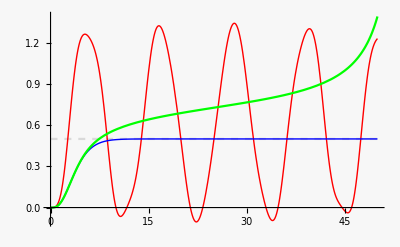

```mathematica
uamp=0.5;
tend=50
yopen=OutputResponse[asys,uamp UnitStep[t],{t,0,tend}];yclosed=OutputResponse[csys,uamp UnitStep[t],{t,0,tend}];
ylin= OutputResponse[csyslin,uamp UnitStep[t],{t,0,tend}];

Plot[{uamp UnitStep[t],yopen,yclosed,ylin},{t,0,tend},PlotRange->All,PlotStyle->{{LightGray,Dashed},{Red,Thick},{Blue,Thick},{Green}}]
```

```mathematica
controller=ℱ[{"OriginalSystemFullController",κ}]//Simplify
```

5 Sin[x_1[t]]-1/2 Sin[2 x_1[t]]+u_1-(-3+Cos[x_1[t]]) x_1[t]+4 Cos[x_1[t]] x_2[t]-Sin[x_1[t]] x_2[t]^2-4 x_3[t]+Cos[x_1[t]] x_3[t]-4 x_4[t]0511NoneNoneFalseFalseFalse{u_1,x_1[t],x_2[t],x_3[t],x_4[t]}Automatic

Calculations to check linearizability

```mathematica
f= ({{Subscript[x, 2], -Sin[Subscript[x, 1]]-Subscript[x, 1]+Subscript[x, 3], Subscript[x, 4], Subscript[x, 1]-Subscript[x, 3]}})[[1]]
```

{x_2,-Sin[x_1]-x_1+x_3,x_4,x_1-x_3}

```mathematica
vars = Array[Subscript[x, #]&, 4]
```

{x_1,x_2,x_3,x_4}

```mathematica
df=D[f,{vars}];MatrixForm[df]
```

(0 | 1 | 0 | 0
-1-Cos[x_1] | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | -1 | 0)

```mathematica
g=Flatten[({{0}, {0}, {0}, {1}})];adfg=-df.g; ad2fg=-df.adfg; ad3fg=-df.ad2fg;  Wc=Join[{g,adfg,ad2fg,ad3fg},2]; Through[{MatrixForm,MatrixRank,Det} [Wc]](* check whether full rank (linearizable) *)
```

{(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | -1
-1 | 0 | 1 | 0),4,1}